```mathematica
X[1] = Subscript[λ, 1]->1/(2 v^2)Sec[β]^2 (mH1sq Cos[a2]^2 Cos[δ]^2-Sin[β]^2 (mAh2sq Cos[γ1]^2+mAh3sq Sin[γ1]^2)+Cos[a3]^2 (mH3sq Cos[δ]^2 Sin[a2]^2+mH2sq Sin[δ]^2)+Sin[a3]^2 (mH2sq Cos[δ]^2 Sin[a2]^2+mH3sq Sin[δ]^2)+(mH2sq-mH3sq) Cos[a3] Sin[a2] Sin[a3] Sin[2 δ]);
```

```mathematica
X[2] = Subscript[λ, 2]->1/(2 v^2)Csc[β]^2 (mH3sq Cos[δ]^2 Sin[a3]^2-Cos[β]^2 (mAh2sq Cos[γ1]^2+mAh3sq Sin[γ1]^2)+(mH1sq Cos[a2]^2+mH2sq Sin[a2]^2 Sin[a3]^2) Sin[δ]^2+Cos[a3]^2 (mH2sq Cos[δ]^2+mH3sq Sin[a2]^2 Sin[δ]^2)+(-mH2sq+mH3sq) Cos[a3] Sin[a2] Sin[a3] Sin[2 δ]);
```

```mathematica
X[3] = Subscript[λ, 3]->1/(8 v^2)(-4 (mAh2sq+mAh3sq-4 mCh)+4 (-mAh2sq+mAh3sq) Cos[2 γ1]+Csc[β] Sec[β] (4 (mH2sq-mH3sq) Cos[2 δ] Sin[a2] Sin[2 a3]+(2 (-2 mH1sq+mH2sq+mH3sq) Cos[a2]^2-(mH2sq-mH3sq) (-3+Cos[2 a2]) Cos[2 a3]) Sin[2 δ]));
```

```mathematica
X[4] = Subscript[λ, 4]->(mAh2sq+mAh3sq-2 mCh+(mAh2sq-mAh3sq) Cos[2 γ1])/v^2;
```

```mathematica
X[5] = Subscript[λ, σ2]->1/(v v3)(Cos[a2] Sec[β] (Cos[δ] Sin[a2] (mH1sq-mH3sq Cos[a3]^2-mH2sq Sin[a3]^2)+(-mH2sq+mH3sq) Cos[a3] Sin[a3] Sin[δ])+(mAh2sq-mAh3sq) Cos[γ1] Sin[γ1] Tan[β]-v (√2 Subscript[α, 1]+2 v3 Subscript[α, 3]) Tan[β]);
```

```mathematica
X[6] = Subscript[λ, σ3]->1/(v v3)((mAh2sq-mAh3sq) Cos[γ1] Cot[β] Sin[γ1]+Cos[a2] Csc[β] ((-mH2sq+mH3sq) Cos[a3] Cos[δ] Sin[a3]+Sin[a2] (-mH1sq+mH3sq Cos[a3]^2+mH2sq Sin[a3]^2) Sin[δ])-v Cot[β] (√2 Subscript[α, 1]+2 v3 Subscript[α, 3]));
```

```mathematica
X[7] = Subscript[λ, σ1]->1/(4 v3^3)(2 v3 (mH1sq Sin[a2]^2+Cos[a2]^2 (mH3sq Cos[a3]^2+mH2sq Sin[a3]^2))+√2 v^2 Cos[β] Sin[β] (Subscript[α, 1]+Subscript[α, 2]));
```

```mathematica
X[8] = Subscript[α, 4]->1/(2 v v3)((-mAh2sq+mAh3sq) Sin[2 γ1]+√2 v Subscript[α, 1]-√2 v Subscript[α, 2]+2 v v3 Subscript[α, 3]);
```

```mathematica
X[9] = Subscript[μ, 3]->1/(4 v)(-v (mAh2sq+mAh3sq+(mAh2sq-mAh3sq) Cos[2 γ1]) Sin[2 β]+(mAh2sq-mAh3sq) v3 Sin[2 γ1]+v v3 (-√2 (3 Subscript[α, 1]+Subscript[α, 2])-4 v3 Subscript[α, 3]));
```

```mathematica
X[10] = Subscript[μ, σb]->1/(4 v3)(-(mAh2sq+mAh3sq) v3+(mAh2sq-mAh3sq) (v3 Cos[2 γ1]+v Sin[2 β] Sin[2 γ1])+v^2 Cos[β] Sin[β] (-3 √2 Subscript[α, 1]+√2 Subscript[α, 2]-8 v3 Subscript[α, 3]));
```

```mathematica
{A1,A2,A3,A4,A5,A6,A7,A8,A9,A10}={X[1][[2]],X[2][[2]],X[3][[2]],X[4][[2]],X[5][[2]],X[6][[2]],X[7][[2]],X[8][[2]],X[9][[2]],X[10][[2]]}/.{v1-> v*Cos[β],v2-> v*Sin[β],v-> 246.,β-> 1.259018458120235,δ-> 0.1446680275363959,v3-> 1000,γ1->0,mH1sq->125.09^2,mH2sq->120^2,mH3sq->300^2,mCh->238.90015346019234^2, mAh2sq ->202.66967872711902^2 ,mAh3sq->202.66967872711902^2 ,Subscript[α, 1]-> 10^-3,Subscript[α, 2]-> 10^-3,Subscript[α, 3]-> 10^-3};
```

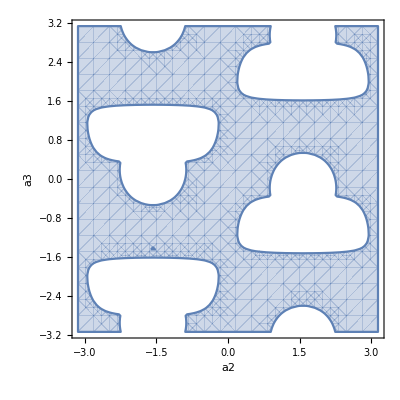

```mathematica
lim = 2;
RegionPlot[Abs[A1]< lim && Abs[A2]< lim && Abs[A3]<lim && Abs[A4]< lim && Abs[A5]< lim && Abs[A6]< lim && Abs[A7]< lim &&Abs[A8]<lim,{a2,-π,π},{a3,-π,π},Axes-> True,AxesLabel->{a2,a3}]
```

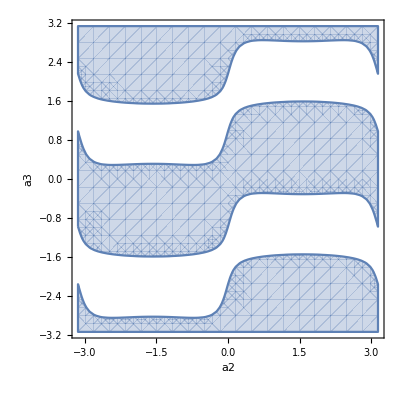

```mathematica
{A1,A2,A3,A4,A5,A6,A7,A8,A9,A10}={X[1][[2]],X[2][[2]],X[3][[2]],X[4][[2]],X[5][[2]],X[6][[2]],X[7][[2]],X[8][[2]],X[9][[2]],X[10][[2]]}/.{v1-> v*Cos[β],v2-> v*Sin[β],v-> 246.,β->ArcTan[1],δ-> 0.1446680275363959,v3-> 9000,γ1->ArcCos[0.1],mH1sq->125.09^2,mH2sq->300^2,mH3sq->500^2,mCh->500^2, mAh2sq ->400^2 ,mAh3sq->501^2 ,Subscript[α, 1]-> 10^-3,Subscript[α, 2]-> 10^-3,Subscript[α, 3]-> 10^-3};
lim = 5;
RegionPlot[Abs[A1]< lim && Abs[A2]< lim && Abs[A3]<lim && Abs[A4]< lim && Abs[A5]< lim && Abs[A6]< lim && Abs[A7]< lim &&Abs[A8]<lim,{a2,-π,π},{a3,-π,π},Axes-> True,AxesLabel->{a2,a3}]
```